# Числено интегриране. Квадратурни формули на Нютон-Коутс

Задача: (a и b са съответно предпоследната и последната цифра от факултетния номер)
Дадена е функцията f(x) = (b + 2 - x)/(2 x^2+a+1)
1. Табулирайте функцията f(x) в интервала [a, a+b+1], като разделите интервала на b+5 равни части.
2. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на левите правоъгълници, използвайки точките получени в 1. Каква е грешката на полученото приближение?
3. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на десните правоъгълници, използвайки точките получени в 1. Каква е грешката на полученото приближение?
4. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на средните правоъгълници, използвайки точките получени в 1. Каква е грешката на полученото приближение?
5. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на трапеците, използвайки точките получени в 1. Каква е грешката на полученото приближение?
6. Може ли по построената в 1 таблица да се използва квадратурната формула на Симпсън за изчисляване на интеграла ∫_a^(a+b+1) f(x)ⅆx? Обосновете отговора си. Ако може, го изчислете и пресметнете каква е грешката на полученото приближение?
7. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на левите правоъгълници с точност 0.00001.
8. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на десните правоъгълници с точност 0.00001.
9. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на средните правоъгълници с точност 0.00001.
10. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на трапеците с точност 0.00001.
11. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на Симпсън с точност 0.00001.

## Съставяне на мрежата

```mathematica
f[x_]:=(9-x)/(2 x^2 + 7)
a = 6.; b = 14.;
h = (b-a)/n;
n = 12;
Print["Мрежата е с брой подинтервали n = ", n, " и стъпка h = ",h]
xt = Table[a + i*h, {i,0,n}]
```

Мрежата е с брой подинтервали n = 12 и стъпка h = 0.666667

{6.,6.66667,7.33333,8.,8.66667,9.33333,10.,10.6667,11.3333,12.,12.6667,13.3333,14.}

```mathematica
f[xt]
```

{0.0379747,0.0243337,0.014549,0.00740741,0.00212014,-0.00183936,-0.00483092,-0.00710564,-0.00884211,-0.0101695,-0.0111826,-0.0119522,-0.0125313}

## Леви правоъгълници

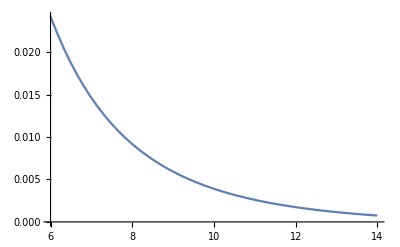

```mathematica
Plot[Abs[f'[x]],{x,a,b}]
```

```mathematica
a = 6.;b= 14.;
h = (b -a)/n;
n = 12;
f[x_]:= (9-x)/(2 x^2 + 7)
Itochno = ∫_a^b f[x]ⅆx ;
I1 = h*∑_(i=0)^(n-1) f[a+i*h];
M1 = Abs[f'[a]];
R1 = (b-a)^2/(2n)*M1;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на левите правоъгълници е ", I1]
Print["Точната стойност                                           е ", Itochno]
Print["Теоретичната грешка по формулата на левите правоъгълници   е ", R1]
Print["Истинската грешка по формулата на левите правоъгълници     е ", Abs[I1-Itochno]]
```

Мрежата е със стъпка 0.666667 и брой подинтервали 12

Приближената стойност по формулата на левите правоъгълници е 0.0203084

Точната стойност                                           е 0.00260677

Теоретичната грешка по формулата на левите правоъгълници   е 0.0645196

Истинската грешка по формулата на левите правоъгълници     е 0.0177016

## Десни правоъгълници

```mathematica
Plot[Abs[f'[x]],{x,a,b}]
```

-Graphics-

```mathematica
a = 6.;b= 14.;
h = (b -a)/n;
n = 12;
f[x_]:= (9-x)/(2 x^2 + 7)
Itochno = ∫_a^b f[x]ⅆx ;
I2 = h*∑_(i=0)^n f[a+i*h];
M2 = Abs[f'[a]];
R2 = (b-a)^2/(2n)*M2;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на левите правоъгълници е ", I2]
Print["Точната стойност                                           е ", Itochno]
Print["Теоретичната грешка по формулата на левите правоъгълници   е ", R2]
Print["Истинската грешка по формулата на левите правоъгълници     е ", Abs[I2-Itochno]]
```

Мрежата е със стъпка 0.666667 и брой подинтервали 12

Приближената стойност по формулата на левите правоъгълници е 0.0119542

Точната стойност                                           е 0.00260677

Теоретичната грешка по формулата на левите правоъгълници   е 0.0645196

Истинската грешка по формулата на левите правоъгълници     е 0.0093474

## Средни правоъгълници

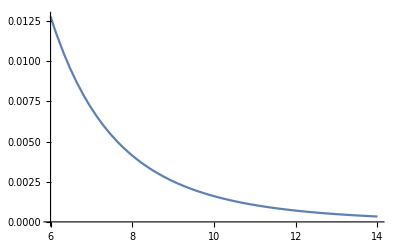

```mathematica
Plot[Abs[f''[x]],{x,a,b}]
```

```mathematica
a = 6.;b= 14.;
h = (b -a)/n;
n = 12;
f[x_]:= (9-x)/(2 x^2 + 7)
Itochno = ∫_a^b f[x]ⅆx ;
I3 = h*∑_(i=0)^(n-1) f[a+i*h + h/2];
M3 = Abs[f''[a]];
R3= (b-a)^3/(24 n^2)*M3;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на левите правоъгълници е ", I3]
Print["Точната стойност                                           е ", Itochno]
Print["Теоретичната грешка по формулата на левите правоъгълници   е ", R3]
Print["Истинската грешка по формулата на левите правоъгълници     е ", Abs[I3-Itochno]]
```

Мрежата е със стъпка 0.666667 и брой подинтервали 12

Приближената стойност по формулата на левите правоъгълници е 0.00217443

Точната стойност                                           е 0.00260677

Теоретичната грешка по формулата на левите правоъгълници   е 0.00189302

Истинската грешка по формулата на левите правоъгълници     е 0.000432339

## Трапеци

```mathematica
Plot[Abs[f''[x]],{x,a,b}]
```

-Graphics-

```mathematica
a = 6.;b= 14.;
h = (b -a)/n;
n = 12;
f[x_]:= (9-x)/(2 x^2 + 7)
Itochno = ∫_a^b f[x]ⅆx ;
IT = h/2*(f[a]+2∑_(i=1)^(n-1) f[a+i*h]+f[b]);
M2 = Abs[f''[a]];
RT = (b-a)^3/(12 n^2)*M2;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на трапците е ", IT]
Print["Точната стойност                               е ", Itochno]
Print["Теоретичната грешка по формулата на трапците   е ", RT]
Print["Истинската грешка по формулата на трапците     е ", Abs[IT-Itochno]]
```

Мрежата е със стъпка 0.666667 и брой подинтервали 12

Приближената стойност по формулата на трапците е 0.00347305

Точната стойност                               е 0.00260677

Теоретичната грешка по формулата на трапците   е 0.00378604

Истинската грешка по формулата на трапците     е 0.00086628

## Симпсън

Може да използваме формулата на Симпсън, тъй като броят на подинтервалите е четно число - в случая 12.

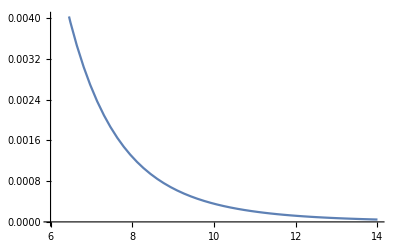

```mathematica
Plot[Abs[f''''[x]],{x,a,b}]
```

```mathematica
a = 6.;b= 14.;
h = (b -a)/n;
n = 12;
f[x_]:= (9-x)/(2 x^2 + 7)
Itochno = ∫_a^b f[x]ⅆx ;
m = n /2;
IS = h/3*(f[a]+4∑_(i=1)^m f[a+(2i-1)*h]+2∑_(i=1)^(m-1) f[a+(2i)*h]+f[b]);
M4 = Abs[f''''[a]];
RS = (b-a)^5/(180 n^4)*M4;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на Симпсън  е ", IS]
Print["Точната стойност                               е ", Itochno]
Print["Теоретичната грешка по формулата на Симпсън    е ", RS]
Print["Истинската грешка по формулата на Симпсън      е ", Abs[IS-Itochno]]
```

Мрежата е със стъпка 0.666667 и брой подинтервали 12

Приближената стойност по формулата на Симпсън  е 0.00261512

Точната стойност                               е 0.00260677

Теоретичната грешка по формулата на Симпсън    е 0.0000509523

Истинската грешка по формулата на Симпсън      е 8.35074×10^-6

# Пресмятане с предварително зададена точност

## Леви правоъгълници

```mathematica
eps = 10^-5;
Clear[n]
Reduce[(b-a)^2/(2n)*M1<=eps, n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n<0||n≥77423.5

```mathematica
a = 6.;b= 14.;
n = 77424;
h = (b -a)/n;
f[x_]:= (9-x)/(2 x^2 + 7)
Itochno = ∫_a^b f[x]ⅆx ;
I1 = h*∑_(i=0)^(n-1) f[a+i*h];
M1 = Abs[f'[a]];
R1 = (b-a)^2/(2n)*M1;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n] 
Print["Приближената стойност по формулата на левите правоъгълници е ", I1]
Print["Точната стойност                                           е ", Itochno]
Print["Теоретичната грешка по формулата на левите правоъгълници   е ", R1]
Print["Истинската грешка по формулата на левите правоъгълници     е ", Abs[I1-Itochno]]
```

Мрежата е със стъпка 0.000103327 и брой подинтервали 77424

Приближената стойност по формулата на левите правоъгълници е 0.00260938

Точната стойност                                           е 0.00260677

Теоретичната грешка по формулата на левите правоъгълници   е 9.99993×10^-6

Истинската грешка по формулата на левите правоъгълници     е 2.60934×10^-6

## Десни правоъгълници

```mathematica
eps = 10^-5;
Clear[n]
Reduce[(b-a)^2/(2n)*M2<=eps, n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n<0||n≥40889.3

```mathematica
a = 6.;b= 14.;
n = 40890;
h = (b -a)/n;
f[x_]:= (9-x)/(2 x^2 + 7)
Itochno = ∫_a^b f[x]ⅆx ;
I2 = h*∑_(i=0)^n f[a+i*h];
M2 = Abs[f'[a]];
R2 = (b-a)^2/(2n)*M2;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n] // N
Print["Приближената стойност по формулата на левите правоъгълници е ", I2]
Print["Точната стойност                                           е ", Itochno]
Print["Теоретичната грешка по формулата на левите правоъгълници   е ", R2]
Print["Истинската грешка по формулата на левите правоъгълници     е ", Abs[I2-Itochno]]
```

Мрежата е със стъпка 0.000195647 и брой подинтервали 40890

Приближената стойност по формулата на левите правоъгълници е 0.00260926

Точната стойност                                           е 0.00260677

Теоретичната грешка по формулата на левите правоъгълници   е 0.0000189346

Истинската грешка по формулата на левите правоъгълници     е 2.48903×10^-6

## Средни правоъгълници

```mathematica
eps = 10^-5;
Clear[n]
Reduce[(b-a)^3/(24 n^2)*M3<=eps, n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n≤-165.105||n≥165.105

```mathematica
a = 6.;b= 14.;
n = 166;
h = (b -a)/n;
f[x_]:= (9-x)/(2 x^2 + 7)
Itochno = ∫_a^b f[x]ⅆx ;
I3 = h*∑_(i=0)^(n-1) f[a+i*h + h/2];
M3 = Abs[f''[a]];
R3= (b-a)^3/(24 n^2)*M3;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на левите правоъгълници е ", I3]
Print["Точната стойност                                           е ", Itochno]
Print["Теоретичната грешка по формулата на левите правоъгълници   е ", R3]
Print["Истинската грешка по формулата на левите правоъгълници     е ", Abs[I3-Itochno]]
```

Мрежата е със стъпка 0.0481928 и брой подинтервали 166

Приближената стойност по формулата на левите правоъгълници е 0.0026045

Точната стойност                                           е 0.00260677

Теоретичната грешка по формулата на левите правоъгълници   е 9.8924×10^-6

Истинската грешка по формулата на левите правоъгълници     е 2.26901×10^-6

## Трапеци

```mathematica
eps = 10^-5;
Clear[n]
Reduce[(b-a)^3/(12 n^2)*M3<=eps, n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n≤-233.493||n≥233.493

```mathematica
a = 6.;b= 14.;
n = 234;
h = (b -a)/n;
f[x_]:= (9-x)/(2 x^2 + 7)
Itochno = ∫_a^b f[x]ⅆx ;
IT = h/2*(f[a]+2∑_(i=1)^(n-1) f[a+i*h]+f[b]);
M2= Abs[f''[a]];
RT = (b-a)^3/(12 n^2)*M2;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на трапците е ", IT]
Print["Точната стойност                               е ", Itochno]
Print["Теоретичната грешка по формулата на трапците   е ", RT]
Print["Истинската грешка по формулата на трапците     е ", Abs[IT-Itochno]]
```

Мрежата е със стъпка 0.034188 и брой подинтервали 234

Приближената стойност по формулата на трапците е 0.00260905

Точната стойност                               е 0.00260677

Теоретичната грешка по формулата на трапците   е 9.95672×10^-6

Истинската грешка по формулата на трапците     е 2.2838×10^-6

## Симпсън

```mathematica
eps = 10^-5;
Clear[n]
Reduce[(b-a)^5/(180 n^4)*M4<=eps, n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n≤-18.029||n≥18.029

```mathematica
a = 6.;b= 14.;
n = 19;
h = (b -a)/n;
f[x_]:= (9-x)/(2 x^2 + 7)
Itochno = ∫_a^b f[x]ⅆx ;
m = n /2;
IS = h/3*(f[a]+4∑_(i=1)^m f[a+(2i-1)*h]+2∑_(i=1)^(m-1) f[a+(2i)*h]+f[b]);
M4 = Abs[f''''[a]];
RS = (b-a)^5/(180 n^4)*M4;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на Симпсън  е ", IS]
Print["Точната стойност                               е ", Itochno]
Print["Теоретичната грешка по формулата на Симпсън    е ", RS]
Print["Истинската грешка по формулата на Симпсън      е ", Abs[IS-Itochno]]
```

Мрежата е със стъпка 0.421053 и брой подинтервали 19

Приближената стойност по формулата на Симпсън  е 0.00776531

Точната стойност                               е 0.00260677

Теоретичната грешка по формулата на Симпсън    е 8.10727×10^-6

Истинската грешка по формулата на Симпсън      е 0.00515854